Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
RS=(GetYodaRaw[NotebookDirectory[]<>"rs.yoda"]);
```

1 Imported ..Histo1D..  /ATLAS_1606_03833/Mgg/0

1 Imported ..Histo1D..  /ATLAS_1606_03833/Mgg/0

1 Imported ..Histo1D..  /ATLAS_1606_03833/Mgg/0

3 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta_inc/0

2 Imported ..Histo1D..  /ATLAS_1407_5063/Mee_eta/0

1 Imported ..Histo1D..  /ATLAS_1407_5063/Mee/0

```mathematica
RS2=GetYodaRaw[NotebookDirectory[]<>"rs_nosmear.yoda"];
```

1 Imported ..Histo1D..  /ATLAS_1606_03833/Mgg/0

This contains Hist1D objects:

OptionValue::nodef: Unknown option TraditionalForm`"PlotStyle" for TraditionalForm`HistogramPlot.

Rescaling Histogram y-Axis with 0.0833333

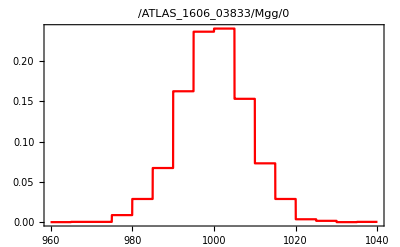

```mathematica
F1=HistogramPlot[RS[[1]],HistScale->0.1/1.2,PlotStyle->{Red}]
```

OptionValue::nodef: Unknown option TraditionalForm`"PlotStyle" for TraditionalForm`HistogramPlot.

Rescaling Histogram y-Axis with 0.038

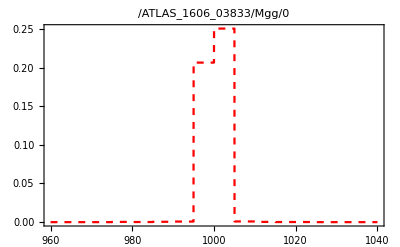

```mathematica
F2=HistogramPlot[RS2[[1]],HistScale->0.038,PlotStyle->{Red,Dashed}]
```

```mathematica
ATLAS=(GetYodaRaw[NotebookDirectory[]<>"ATLAS_rs.yoda"]);
```

1 Imported ..Scatter2D..  /REF/d01-x01-y01

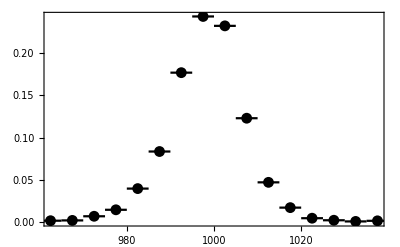

```mathematica
F3=ScatterPlot[ATLAS[[1]],PlotStyle->{Black}]
```

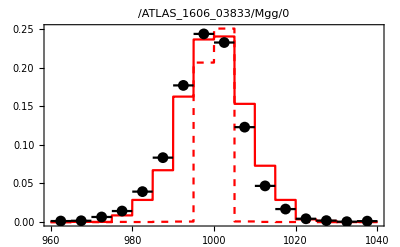

```mathematica
Show[{F1,F2,F3}]
```

```mathematica
Export["~/Desktop/mgg.png",%]
```

~/Desktop/mgg.png